## Computation of the EoS depending on h (PwP with Sly)

### Werte :

```mathematica
NN=3;
Γ0 =1.35692395;
K0=3.594 10^13/uK;
P1=10^(34.348)/up;
Γi={Γ0,3.005,2.988,2.851};
Ki={K0,0,0,0};
ρi={0,0,1.85,3.7}ρnuc/uρ;
```

### Definitionen :

```mathematica
uc=2.99792458 10^10;
uG=6.67384 10^(-8);
uM=1.9891 10^33;
ut=uG*uM/uc^3;
ul=uG*uM/uc^2;
up=uM/(ut*ut*ul);
uρ=uM/ul^3;
uK=up/uρ^Γ0;
ρnuc=2.7 10^14;
```

```mathematica
P[ρ_,i_]:=Ki[[i]]ρ^Γi[[i]];
Eps[ρ_,i_]:=(1+ai[[i]])ρ+Ki[[i]]/(Γi[[i]]-1)ρ^Γi[[i]];
```

### Compute K_i,a_i,p_i,ϵ_i :

```mathematica
Ki[[2]]=P1 /ρi[[3]]^Γi[[2]];
ρi[[2]]=(Ki[[1]]/Ki[[2]])^(1/(Γi[[2]]-Γi[[1]]));
For[i=2,i≤NN,i++, 
Ki[[i+1]]=Ki[[i]]*ρi[[i+1]]^(Γi[[i]]-Γi[[i+1]]);
]
```

```mathematica
ai={0,0,0,0};
pi={0,0,0,0};
ϵi={0,0,0,0};
For[i=2,i≤NN+1,i++, 
pi[[i]]=P[ρi[[i]],i];
ϵi[[i]]=Eps[ρi[[i]],i];
ϵi[[i-1]]=Eps[ρi[[i-1]],i-1];
ai[[i]]=-Ki[[i]]/(Γi[[i]]-1)ρi[[i-1]]^Γi[[i-1]];
If[i>2,ai[[i]]=ai[[i]]+ϵi[[i-1]]/ρi[[i-1]]-1,1];
]
```

### Compute h (p) and p (h)

```mathematica
R[p_]:=(p/K)^(1/Γ);
h1[p2_]:=Integrate[1/(R[p]+p),{p,0,p2},Assumptions->{p2>0,K>0,Γ>1}];h2[p2_]:=Integrate[1/(R[p]+p),{p,p1,p2},Assumptions->{p1>0,p2>0,K>0,Γ>1}];
```

```mathematica
h1[p1]
h2[p2]
hi={h1[p]/.{p->pi[[2]],Γ->Γi[[1]],K->Ki[[1]]},
h2[p]/.{p1->pi[[2]],p->pi[[3]],Γ->Γi[[2]],K->Ki[[2]]},
h2[p]/.{p1->pi[[3]],p->pi[[4]],Γ->Γi[[3]],K->Ki[[3]]}}
```

(Γ Log[1+K^(1/Γ) p1^((-1+Γ)/Γ)])/(-1+Γ)

(Log[p1]-Γ Log[p1+(p1/K)^(1/Γ)]-Log[p2]+Γ Log[p2+(p2/K)^(1/Γ)])/(-1+Γ)

$Aborted

```mathematica
h2[p2]//FullSimplify
```

(Log[p1]-Log[p2]+Γ Log[(p2+(p2/K)^(1/Γ))/(p1+(p1/K)^(1/Γ))])/(-1+Γ)

### Plot stuff :

```mathematica
Pl1=LogPlot[P[ρ,1],{ρ,ρi[[1]],ρi[[2]]},PlotStyle->Red];
Pl2=LogPlot[P[ρ,2],{ρ,ρi[[2]],ρi[[3]]},PlotStyle->Blue];
Pl3=LogPlot[P[ρ,3],{ρ,ρi[[3]],ρi[[4]]},PlotStyle->Green];
Pl4=LogPlot[P[ρ,4],{ρ,ρi[[4]],1.5*ρi[[4]]},PlotStyle->Black];
```

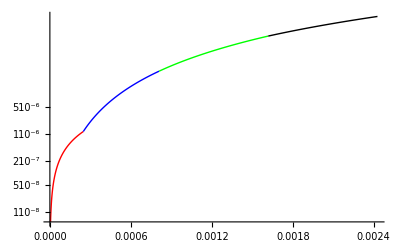

```mathematica
Show[{Pl1,Pl2,Pl3,Pl4},PlotRange->All]
```

```mathematica
Pl1=Plot[Evaluate[h1[p]/.{Γ->Γi[[1]],K->Ki[[1]]}],{p,pi[[1]],pi[[2]]},PlotStyle->Red];
Pl2=Plot[Evaluate[hi[[1]]+h2[p]/.{p1->pi[[2]],Γ->Γi[[2]],K->Ki[[2]]}],{p,pi[[2]],pi[[3]]},PlotStyle->Blue];
Pl3=Plot[Evaluate[hi[[1]]+hi[[2]]+h2[p]/.{p1->pi[[3]],Γ->Γi[[3]],K->Ki[[3]]}],{p,pi[[3]],pi[[4]]},PlotStyle->Green];
Pl4=Plot[Evaluate[hi[[1]]+hi[[2]]+hi[[3]]+h2[p]/.{p1->pi[[4]],Γ->Γi[[4]],K->Ki[[4]]}],{p,pi[[4]],1.5*pi[[4]]},PlotStyle->Black];
```

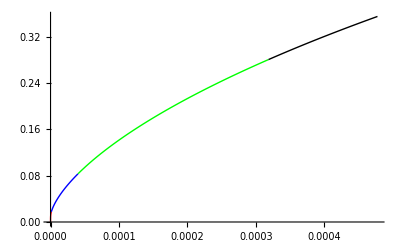

```mathematica
Show[{Pl1,Pl2,Pl3,Pl4},PlotRange->All]
```

### Results :

```mathematica
Γi
Ki
ρi
pi
```

{1.35692,3.005,2.988,2.851}

{0.0894924,78555.9,69601.1,28857.6}

{0,0.000247593,0.000809193,0.00161839}

{0,1.14384×10^-6,0.0000401675,0.000318678}

### Zeugs :

```mathematica
H=Evaluate[h2[p]]
```

(-Log[p]+Log[p1]+Γ Log[(p+(p/K)^(1/Γ))/(p1+(p1/K)^(1/Γ))])/(-1+Γ)

```mathematica
Solve[H==h,Log[p]]
```

{{Log[p]→h-h Γ+Log[p1]+Γ Log[(p+(p/K)^(1/Γ))/(p1+(p1/K)^(1/Γ))]}}

```mathematica
D[H,p]//FullSimplify
```

1/(p+(p/K)^(1/Γ))

```mathematica
Solve[h==(Γ Log[1+K^(1/Γ) p1^((-1+Γ)/Γ)])/(-1+Γ),p1]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{p1→(-(1-ⅇ^(h-h/Γ)) K^(-1/Γ))^(Γ/(-1+Γ))}}